## R0 calculations

#### Setting up some simulations to look at how changing R0 will change the results. Goal here is to: 1. Loop over R0 ∈ {0.8,1.0,…,2.6} 2. For each R0R0​, compute: extinction time per run mean & variance of infected counts over time max proportion infected epidemic size duration above threshold (e.g. It>10It​>10) 3. Aggregate summary statistics across 1000 simulations

```mathematica
(* 1. PARAMETERS AND SETUP --------------------------------------------------- *)

ClearAll["Global`*"]
SeedRandom[123]; (* set seed so stuff is reproducible *)

numPatches = 1000; (* number of spatial patches *)
initialInfected = 1; (* start with just one infected person *)
r0Values = Range[0.8, 2.6, 0.2]; (* range of quasi-r0 values *)
numReps = 1000; (* how many runs to average over *)
maxTime = 1000; (* max timesteps per run *)
threshold = 100; (* for tracking how long the outbreak stays "big" *)
weights = ConstantArray[1/numPatches, numPatches]; (* uniform patch weight *)

(* 2. FUNCTION TO RUN ONE SIMULATION ----------------------------------------- *)

simulateRun[totalIndividuals_] := Module[
  {
    t = 0, NI = initialInfected, NT = totalIndividuals,
    infectedHistory = {}, Sloc, Iloc, cloc
  },

  (* while there's still infecteds and we haven't hit time limit *)
  While[NI > 0 && t < maxTime,
  
    (* randomly assign susceptibles and infecteds to patches *)
    Sloc = RandomChoice[weights -> Range[1, numPatches], NT - NI];
    Iloc = RandomChoice[weights -> Range[1, numPatches], NI];

    (* get list of patch IDs that have both S and I *)
    cloc = Intersection[Sloc, Iloc];

    (* count how many susceptibles were in those shared patches = new infecteds *)
    NI = Total[Count[Sloc, #] & /@ cloc];

    (* store current number of infecteds *)
    infectedHistory = Append[infectedHistory, NI];
    t++
  ];

  (* return summary stats for the run *)
  <|
    "ExtinctionTime" -> t,
    "InfectedTimeSeries" -> infectedHistory,
    "MaxProportionInfected" -> Max[infectedHistory]/totalIndividuals,
    "EpidemicSize" -> Total[infectedHistory],
    "DurationAboveThreshold" -> Count[infectedHistory, x_ /; x > threshold]
  |>
]
```

### Run the simulations if needed or READ THEM FROM A FILE below this chunk

```mathematica
(* 3. MAIN LOOP TO RUN SIMULATIONS FOR EACH R0 ------------------------------- *)

simulationResults = Association[];

Do[
  Module[
    {
      Nt = Round[r0 * numPatches + initialInfected],
      counter = 0, results, extinctionTimes, timeSeriesList,
      propMax, sizes, durations, aligned, meanOverTime, varOverTime, maxLen
    },

    Print["Running simulations for R₀ = ", r0, " (Nt = ", Nt, ")..."];
    SetSharedVariable[counter]; (* so progress bar works in parallel *)
    (* run a bunch of simulations in parallel *)
    results = Monitor[
      ParallelTable[
        Module[{out = simulateRun[Nt]},
          counter++;
          out
        ],
        {numReps}
      ],
      Row[{
        "Progress: ", counter, "/", numReps, " (", 
        Round[100.0 * counter / numReps], "%)"
      }]
    ];
    (* unpack and process all results *)
    extinctionTimes = results[[All, "ExtinctionTime"]];
    timeSeriesList = results[[All, "InfectedTimeSeries"]];
    propMax = results[[All, "MaxProportionInfected"]];
    sizes = results[[All, "EpidemicSize"]];
    durations = results[[All, "DurationAboveThreshold"]];

    (* make all time series same length so we can average them *)
    maxLen = Min[maxTime, Max[Length /@ timeSeriesList]];
    aligned = Transpose[PadRight[#, maxLen, 0] & /@ timeSeriesList];

    (* mean and variance of infected through time *)
    meanOverTime = Mean /@ aligned;
    varOverTime = Variance /@ aligned;

    (* store all stats in an assoc keyed by R0 *)
simulationResults[r0] = <|
  "ExtinctionTimes" -> extinctionTimes,
  "InfectedTimeSeries" -> timeSeriesList, (* <<< ADD THIS LINE *)
  "MeanInfectedOverTime" -> meanOverTime,
  "VarianceInfectedOverTime" -> varOverTime,
  "MaxProportionInfected" -> propMax,
  "EpidemicSizes" -> sizes,
  "DurationsAboveThreshold" -> durations,
  "ExtinctionProbability" -> Count[extinctionTimes, t_ /; t < maxTime]/numReps
|>;

  ],
  {r0, r0Values}
];
(* checking size/type of object for saving *)
(*Head[simulationResults]
ByteCount[simulationResults]
NotebookDirectory[]*)
Export[
  FileNameJoin[
    {NotebookDirectory[], "..", "..", "outputs", "intermediate-obs", "simResults.wl"}
  ],
  simulationResults
]
```

Running simulations for R₀ = 0.8 (Nt = 801)...

Running simulations for R₀ = 1. (Nt = 1001)...

Running simulations for R₀ = 1.2 (Nt = 1201)...

Running simulations for R₀ = 1.4 (Nt = 1401)...

Running simulations for R₀ = 1.6 (Nt = 1601)...

Running simulations for R₀ = 1.8 (Nt = 1801)...

Running simulations for R₀ = 2. (Nt = 2001)...

Running simulations for R₀ = 2.2 (Nt = 2201)...

Running simulations for R₀ = 2.4 (Nt = 2401)...

Running simulations for R₀ = 2.6 (Nt = 2601)...

```mathematica
simulationResults
```

```mathematica
(* read in instead of re-running *)
If[
  !ValueQ[simResults], 
  simulationResults = Import[
    FileNameJoin[
      {NotebookDirectory[], "..", "..", "outputs", "intermediate-obs", "simResults.wl"}
    ]
  ]
]
```

#### Let’s get a summary table so we can see roughly what the results say:

```mathematica
CI95[data_] := Quantile[data, {0.025, 0.975}];

summarizeR0[r_] := Module[
  {
    ext = simulationResults[r]["ExtinctionTimes"],
    epi = simulationResults[r]["EpidemicSizes"],
    dur = simulationResults[r]["DurationsAboveThreshold"],
    extCI, epiCI, durCI, varExt, varEpi, varDur
  },
  
  extCI = CI95[ext];
  epiCI = CI95[epi];
  durCI = CI95[dur];
  varExt = Variance[ext];
  varEpi = Variance[epi];
  varDur = Variance[dur];
  
  With[{round = Round[#, 0.01] &},  (* round to 2 decimal places *)
    {
      r,
      round@Mean[ext], round@extCI[[1]], round@extCI[[2]],
      round@Mean[epi], round@epiCI[[1]], round@epiCI[[2]],
      round@Mean[dur], round@durCI[[1]], round@durCI[[2]],
      round@varExt, round@varEpi, round@varDur
    }
  ]
];

summaryData = Prepend[
  summarizeR0 /@ r0Values,
  {
    "R₀",
    "Mean time to I=0", "I=0 CI Low", "I=0 CI High",
    "Mean Size", "CI Low", "CI High",
    "Mean Duration", "CI Low", "CI High", 
    "Var Time", "Var Size", "Var Duration"
  }
];
Grid[
  summaryData,
  Frame -> All,
  Alignment -> Center,
  Background -> {None, {LightGray, {}}},
  ItemStyle -> Directive[FontFamily -> "Helvetica", 12]
]
```

R₀ | Mean time to I=0 | I=0 CI Low | I=0 CI High | Mean Size | CI Low | CI High | Mean Duration | CI Low | CI High | Var Time | Var Size | Var Duration
0.8 | 2.93 | 1. | 11. | 3.99 | 0. | 28. | 0. | 0. | 0. | 10.47 | 102.26 | 0.
1. | 7.92 | 1. | 51. | 50.66 | 0. | 443. | 0. | 0. | 0. | 304.96 | 53741.6 | 0.
1.2 | 293.25 | 1. | 1000. | 37178.4 | 0. | 131150. | 265.58 | 0. | 938. | 205224. | 3.37168×10^9 | 172155.
1.4 | 523.14 | 1. | 1000. | 134956. | 0. | 261259. | 514.79 | 0. | 991. | 248581. | 1.66955×10^10 | 242925.
1.6 | 628.77 | 1. | 1000. | 243032. | 0. | 389414. | 621.87 | 0. | 994. | 232883. | 3.50232×10^10 | 229310.
1.8 | 734.46 | 1. | 1000. | 377054. | 0. | 515893. | 728.28 | 0. | 995. | 194770. | 5.15746×10^10 | 192408.
2. | 780.35 | 1. | 1000. | 498223. | 0. | 641002. | 774.93 | 0. | 996. | 171232. | 7.00836×10^10 | 169546.
2.2 | 844.23 | 1. | 1000. | 643358. | 0. | 764374. | 839.27 | 0. | 996. | 131406. | 7.65825×10^10 | 130325.
2.4 | 864.17 | 1. | 1000. | 763951. | 0. | 886351. | 859.62 | 0. | 996. | 117323. | 9.19594×10^10 | 116432.
2.6 | 911.12 | 1. | 1000. | 915503. | 0. | 1.00698×10^6 | 906.86 | 0. | 997. | 80948.8 | 8.19657×10^10 | 80425.

### Plotting the results from the simulations:

#### We want plots that show: 1) the histogram of time to I = 0 for each value of R0

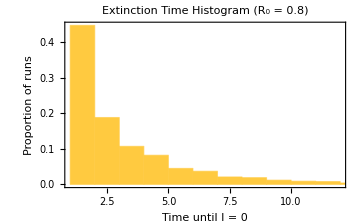

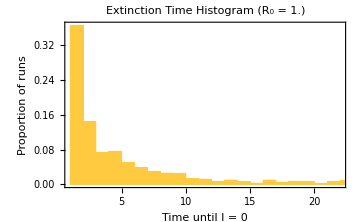

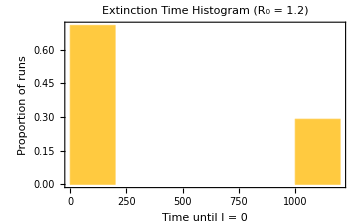

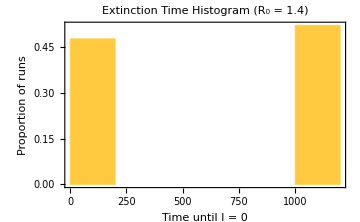

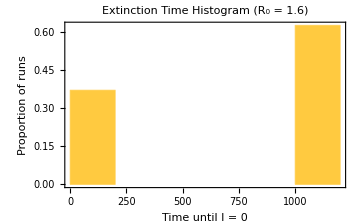

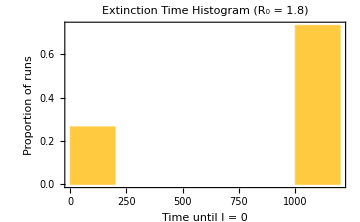

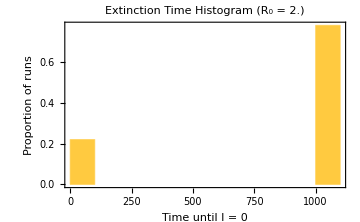

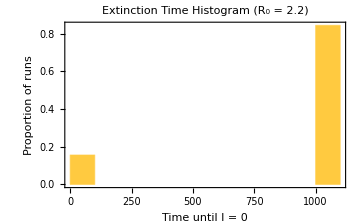

```mathematica
(* 4. PLOT HISTOGRAMS OF EXTINCTION TIME BY R₀ ------------------------------- *)
Do[
  Module[{extTimes, hist},
    extTimes = simulationResults[r0]["ExtinctionTimes"];
    (* simple histogram for this r0 *)
    hist = Histogram[
      extTimes,
      Automatic, (* binning *)
      "Probability", (* normalize to probs *)
      PlotLabel -> Row[{"Extinction Time Histogram (R₀ = ", r0, ")"}],
      Frame -> True,
      FrameLabel -> {"Time until I = 0", "Proportion of runs"},
      ImageSize -> Medium
    ];

    Print[hist];
  ],
  {r0, r0Values}
];
```

#### 2) the mean extinction time per R0

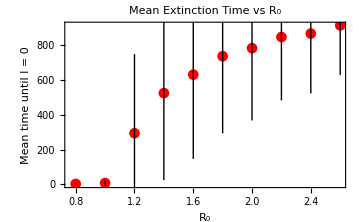

```mathematica
(* 5. MEAN EXTINCTION TIME VS R₀ (with error bars drawn manually) ------------ *)

Module[
  {rVals, means, stds, basePoints, errorBars, plot},

  rVals = r0Values;
  means = Mean /@ (simulationResults[#]["ExtinctionTimes"] & /@ rVals);
  stds = StandardDeviation /@ (simulationResults[#]["ExtinctionTimes"] & /@ rVals);

  basePoints = Transpose[{rVals, means}];

  (* draw vertical error bars manually using Line[] *)
  errorBars = Table[
    {
      Black,
      Line[{{rVals[[i]], means[[i]] - stds[[i]]}, {rVals[[i]], means[[i]] + stds[[i]]}}]
    },
    {i, Length[rVals]}
  ];

  plot = Show[
    ListPlot[
      basePoints,
      PlotStyle -> Red,
      PlotMarkers -> Automatic,
      Frame -> True,
      FrameLabel -> {"R₀", "Mean time until I = 0"},
      PlotLabel -> "Mean Extinction Time vs R₀",
      ImageSize -> Medium
    ],
    Graphics[errorBars]
  ];

  Print[plot];
]
```

#### 3) A timeseries showing I vs S through time (mostly a sanity check / curiousity)

```mathematica
(* 6. PLOT I AND S OVER TIME FOR R₀ = 1.0 WITH RIBBONS ---------------------- *)

r0 = 1.0;

(* grab list of I time series *)
infectedSeriesList = simulationResults[r0]["MeanInfectedOverTime"];

(* check length of first few time series *)
Table[Length[infectedSeriesList[[i]]], {i, 1, 5}]

maxLen = Max[Length /@ infectedSeriesList];

alignedI = PadRight[#, maxLen, 0] & /@ infectedSeriesList;

MatrixForm[alignedI[[1 ;; 5]]] (* check first 5 rows *)
(*Module[
  {
    r0 = 1.0,
    Nt, Iseries, maxLen, alignedI, meanI, stdI,
    meanS, stdS, timeVec, infectedRibbon, susceptibleRibbon, lines, plot
  },

  Nt = Round[r0 * numPatches + initialInfected];
  Iseries = simulationResults[r0]["MeanInfectedOverTime"];
  maxLen = Length[Iseries];
  timeVec = Range[0, maxLen - 1]; (* start at time 0 *)

  (* get all time series aligned *)
  alignedI = Transpose[
    PadRight[#, maxLen, 0] & /@ 
      (simulationResults[r0]["InfectedTimeSeries"])
  ];

  (* compute mean and std dev for I *)
  meanI = Mean /@ alignedI;
  stdI = StandardDeviation /@ alignedI;

  (* compute S = N - I and its sd *)
  meanS = Nt - meanI;
  stdS = stdI; (* same because var(S) = var(I), since N is constant *)

  (* ribbon polygons for shaded error bands *)
  infectedRibbon = {
    LightRed,
    Polygon[
      Join[
        Transpose[{timeVec, meanI - stdI}],
        Reverse[Transpose[{timeVec, meanI + stdI}]]
      ]
    ]
  };

  susceptibleRibbon = {
    LightBlue,
    Polygon[
      Join[
        Transpose[{timeVec, meanS - stdS}],
        Reverse[Transpose[{timeVec, meanS + stdS}]]
      ]
    ]
  };

  (* lines for mean I and S *)
  lines = {
    Red, Thick, Line[Transpose[{timeVec, meanI}]],
    Blue, Thick, Line[Transpose[{timeVec, meanS}]]
  };

  (* combine into one plot *)
  plot = Show[
    Graphics[{infectedRibbon, susceptibleRibbon, lines}],
    Frame -> True,
    FrameLabel -> {"Time", "Number of Individuals"},
    PlotLabel -> "I and S over time (R₀ = 1.0)",
    ImageSize -> Medium
  ];

  Print[plot];
]*)
```

{0,0,0,0,0}

PadRight::normal: Nonatomic expression expected at position 1 in PadRight[1013/1000,0,0].

PadRight::normal: Nonatomic expression expected at position 1 in PadRight[43/40,0,0].

PadRight::normal: Nonatomic expression expected at position 1 in PadRight[533/500,0,0].

General::stop: Further output of PadRight::normal will be suppressed during this calculation.

(PadRight[1013/1000,0,0]
PadRight[43/40,0,0]
PadRight[533/500,0,0]
PadRight[263/250,0,0]
PadRight[1009/1000,0,0])

### Setting up some simulations to look at how changing R0 will change the results:

#### First I’ll make a function that generates the weights in a variable way in case I want to change it later:

```mathematica
generateWeights[type_, numPatches_, q_: 0] := Module[{w},
  Switch[type,

    (* equal chance for every patch, nothing fancy *)
    "constant", ConstantArray[1/numPatches, numPatches],

    (* uniform probs, centered at 1/n but wiggly by q *)
    "uniform", Normalize[
      RandomVariate[
        UniformDistribution[{1/numPatches - q, 1/numPatches + q}], 
        numPatches
      ]
    ],

    (* exponential weights, avg is still 1/n *)
    "exponential", Normalize[
      RandomVariate[ExponentialDistribution[numPatches], numPatches]
    ]
  ]
];
```

#### Goal here is to: 1. Loop over R0 ∈ {0.8,1.0,…,2.6} 2. For each R0R0​, compute: extinction time per run mean & variance of infected counts over time max proportion infected epidemic size duration above threshold (e.g. It>10It​>10) 3. Aggregate summary statistics across 1000 simulations

```mathematica
(* PARAMETERS *)
ClearAll["Global`*"]
SeedRandom[123];

numPatches = 1000;
initialInfected = 1;
r0Values = Range[0.8, 2.6, 0.2];
numReps = 1000;
maxTime = 1000;
threshold = 100; (*This is a threshold counter to see for how long each sim stays above this number of indI*)
weights = ConstantArray[1/numPatches, numPatches];

(* FUNCTION TO RUN A SINGLE SIMULATION *)
simulateRun[totalIndividuals_] := Module[
  {t = 0, NI = initialInfected, NT = totalIndividuals, infectedHistory = {}, Sloc, Iloc, cloc, infectedEver = <||>},

  While[NI > 0 && t < maxTime,
    Sloc = RandomChoice[weights -> Range[1, numPatches], NT - NI];
    Iloc = RandomChoice[weights -> Range[1, numPatches], NI];
    cloc = Intersection[Sloc, Iloc];

    NI = Total[Count[Sloc, #] & /@ cloc];
    infectedHistory = Append[infectedHistory, NI];
    t++
  ];

  <|
    "ExtinctionTime" -> t,
    "InfectedTimeSeries" -> infectedHistory,
    "MaxProportionInfected" -> Max[infectedHistory]/totalIndividuals,
    "EpidemicSize" -> Total[infectedHistory],
    "DurationAboveThreshold" -> Count[infectedHistory, x_ /; x > threshold]
  |>
]

(* MAIN LOOP OVER R0 VALUES *)
simulationResults = Association[];

Do[
  Module[{Nt, counter = 0, progress, results, extinctionTimes, timeSeriesList, 
  propMax, sizes, durations, aligned, meanOverTime, varOverTime},
    Nt = Round[r0 * numPatches + initialInfected];
    Print["Running simulations for R₀ = ", r0, " (Nt = ", Nt, ")..."];
    (* Shared progress counter *)
    SetSharedVariable[counter];
    results = Monitor[
      ParallelTable[
        Module[{out = simulateRun[Nt]},
          counter++;
          out
        ],
        {numReps}
      ],
      Row[{
        "Progress: ", counter, "/", numReps, " (", 
        Round[100.0*counter/numReps], "%)"
      }]
    ];

    (* Extract summary data *)
    extinctionTimes = results[[All, "ExtinctionTime"]];
    timeSeriesList = results[[All, "InfectedTimeSeries"]];
    propMax = results[[All, "MaxProportionInfected"]];
    sizes = results[[All, "EpidemicSize"]];
    durations = results[[All, "DurationAboveThreshold"]];

    (* Align time series and compute mean/variance *)
    maxLen = Min[maxTime, Max[Length /@ timeSeriesList]];
    aligned = Transpose[PadRight[#, maxLen, 0] & /@ timeSeriesList];
    meanOverTime = Mean /@ aligned;
    varOverTime = Variance /@ aligned;

    simulationResults[r0] = <|
      "ExtinctionTimes" -> extinctionTimes,
      "MeanInfectedOverTime" -> meanOverTime,
      "VarianceInfectedOverTime" -> varOverTime,
      "MaxProportionInfected" -> propMax,
      "EpidemicSizes" -> sizes,
      "DurationsAboveThreshold" -> durations,
      "ExtinctionProbability" -> Count[extinctionTimes, t_ /; t < maxTime]/numReps
    |>;
  ],
  {r0, r0Values}
];
```

Running simulations for R₀ = 0.8 (Nt = 801)...

Running simulations for R₀ = 1. (Nt = 1001)...

Running simulations for R₀ = 1.2 (Nt = 1201)...

Running simulations for R₀ = 1.4 (Nt = 1401)...

Running simulations for R₀ = 1.6 (Nt = 1601)...

Running simulations for R₀ = 1.8 (Nt = 1801)...

Running simulations for R₀ = 2. (Nt = 2001)...

Running simulations for R₀ = 2.2 (Nt = 2201)...

Running simulations for R₀ = 2.4 (Nt = 2401)...

Running simulations for R₀ = 2.6 (Nt = 2601)...

```mathematica
CI95[data_] := Quantile[data, {0.025, 0.975}];

summarizeR0[r_] := Module[
  {
    ext = simulationResults[r]["ExtinctionTimes"],
    epi = simulationResults[r]["EpidemicSizes"],
    dur = simulationResults[r]["DurationsAboveThreshold"],
    extCI, epiCI, durCI, varExt, varEpi, varDur
  },
  
  extCI = CI95[ext];
  epiCI = CI95[epi];
  durCI = CI95[dur];
  varExt = Variance[ext];
  varEpi = Variance[epi];
  varDur = Variance[dur];
  
  With[{round = Round[#, 0.01] &},  (* round to 2 decimal places *)
    {
      r,
      round@Mean[ext], round@extCI[[1]], round@extCI[[2]],
      round@Mean[epi], round@epiCI[[1]], round@epiCI[[2]],
      round@Mean[dur], round@durCI[[1]], round@durCI[[2]],
      round@varExt, round@varEpi, round@varDur
    }
  ]
];

summaryData = Prepend[
  summarizeR0 /@ r0Values,
  {
    "R₀",
    "Mean time to I=0", "I=0 CI Low", "I=0 CI High",
    "Mean Size", "CI Low", "CI High",
    "Mean Duration", "CI Low", "CI High", 
    "Var Time", "Var Size", "Var Duration"
  }
];
Grid[
  summaryData,
  Frame -> All,
  Alignment -> Center,
  Background -> {None, {LightGray, {}}},
  ItemStyle -> Directive[FontFamily -> "Helvetica", 12]
]
```

R₀ | Mean time to I=0 | I=0 CI Low | I=0 CI High | Mean Size | CI Low | CI High | Mean Duration | CI Low | CI High | Var Time | Var Size | Var Duration
0.8 | 2.85 | 1. | 11. | 3.71 | 0. | 25. | 0. | 0. | 0. | 8.34 | 69.41 | 0.
1. | 7.22 | 1. | 47. | 41.72 | 0. | 314. | 0. | 0. | 0. | 259.11 | 43714.3 | 0.
1.2 | 290.22 | 1. | 1000. | 36802.8 | 0. | 130807. | 263.44 | 0. | 940. | 203992. | 3.35236×10^9 | 171872.
1.4 | 538.07 | 1. | 1000. | 138860. | 0. | 261185. | 529.74 | 0. | 991. | 247736. | 1.66426×10^10 | 242207.
1.6 | 646.69 | 1. | 1000. | 249975. | 0. | 389336. | 639.65 | 0. | 993. | 228017. | 3.42778×10^10 | 224436.
1.8 | 740.43 | 1. | 1000. | 380112. | 0. | 516118. | 734.26 | 0. | 995. | 191959. | 5.0817×10^10 | 189622.
2. | 785.33 | 1. | 1000. | 501412. | 0. | 640949. | 779.87 | 0. | 995. | 168431. | 6.89287×10^10 | 166746.
2.2 | 844.24 | 1. | 1000. | 643283. | 0. | 764292. | 839.24 | 0. | 996. | 131392. | 7.65645×10^10 | 130314.
2.4 | 885.17 | 1. | 1000. | 782593. | 0. | 886383. | 880.58 | 0. | 996. | 101583. | 7.96651×10^10 | 100863.
2.6 | 883.15 | 1. | 1000. | 887363. | 0. | 1.0069×10^6 | 878.97 | 0. | 997. | 103155. | 1.0444×10^11 | 102474.

#### Plot the mean time I = 0 (with 95% CI’s)

```mathematica
(* Helper for confidence intervals *)
CI95[data_] := Quantile[data, {0.025, 0.975}];

(* Mean extinction time + 95% CI *)
extinctionStatsAssoc = Table[
  Module[{vals = simulationResults[r]["ExtinctionTimes"], ci},
    ci = CI95[vals];
    <|
      "R0" -> r,
      "MeanTime" -> N[Mean[vals]],
      "CI_Lower" -> N[ci[[1]]],
      "CI_Upper" -> N[ci[[2]]]
    |>
  ],
  {r, r0Values}
];
extinctionStatsAssoc

(*(* Colour pallette *)
colorFunc = ColorData["Temperature"];
meanTimes = extinctionStatsAssoc[[All, "MeanTime"]];
minVal = Min[meanTimes];
maxVal = Max[meanTimes];
(* Normalize mean time to [0,1] for color mapping *)
normalize[val_] := (val - minVal)/(maxVal - minVal)


coloredPoints = Table[
  {
    colorFunc[normalize[stat["MeanTime"]]],
    PointSize[Medium],
    Point[{stat["R0"], stat["MeanTime"]}],
    (* vertical error bar *)
    Gray,
    Line[{
      {stat["R0"], stat["CI_Lower"]},
      {stat["R0"], stat["CI_Upper"]}
    }]
  },
  {stat, extinctionStatsAssoc}
]

Graphics[
  coloredPoints /. PointSize[_] :> PointSize[Large],
  Frame -> True,
  FrameLabel -> {
    Style["R₀", 14],
    Style["Mean Time to I=0", 14]
  },
  PlotRange -> {{0.75, 2.65}, Automatic},  
  AspectRatio -> 0.5,                     
  ImageSize -> Large,
  FrameTicks -> Automatic,
  GridLines -> None
]*)
```

Table::iterb: Iterator {r,r0Values} does not have appropriate bounds.

Table[Module[{vals=simulationResults[r][ExtinctionTimes],ci},ci=CI95[vals];Association[R0→r,MeanTime→N[Mean[vals]],CI_Lower→N[ci⟦1⟧],CI_Upper→N[ci⟦2⟧]]],{r,r0Values}]

#### Plot mean and CI epidemic sizes

{{RGBColor[0.405188, 0.204349, 0.343389],PointSize[Medium],Point[{0.8,0.00154557}],GrayLevel[0.5],Line[{{0.8,0.},{0.8,0.00749064}}]},{RGBColor[0.41013165360264336, 0.20472893446197718, 0.3437209498545647],PointSize[Medium],Point[{1.,0.0029001}],GrayLevel[0.5],Line[{{1.,0.},{1.,0.01998}}]},{RGBColor[0.5848496275413837, 0.21909568148235217, 0.3565467385876576],PointSize[Medium],Point[{1.2,0.0508976}],GrayLevel[0.5],Line[{{1.2,0.},{1.2,0.167361}}]},{RGBColor[0.7730493744883217, 0.3136864320659444, 0.45194098771400126],PointSize[Medium],Point[{1.4,0.115826}],GrayLevel[0.5],Line[{{1.4,0.},{1.4,0.242684}}]},{RGBColor[0.8310764426802314, 0.5065485307747168, 0.6366237191993249],PointSize[Medium],Point[{1.6,0.184844}],GrayLevel[0.5],Line[{{1.6,0.},{1.6,0.293567}}]},{RGBColor[0.764819803310644, 0.6424074563543393, 0.7799465263783234],PointSize[Medium],Point[{1.8,0.242963}],GrayLevel[0.5],Line[{{1.8,0.},{1.8,0.335369}}]},{RGBColor[0.6958754650988991, 0.7302766714413461, 0.8606711547919346],PointSize[Medium],Point[{2.,0.290625}],GrayLevel[0.5],Line[{{2.,0.},{2.,0.366317}}]},{RGBColor[0.6789905244955493, 0.8057123545778285, 0.8971667531251799],PointSize[Medium],Point[{2.2,0.326224}],GrayLevel[0.5],Line[{{2.2,0.},{2.2,0.392095}}]},{RGBColor[0.6667150320703114, 0.8505158704703555, 0.8965233174601511],PointSize[Medium],Point[{2.4,0.360993}],GrayLevel[0.5],Line[{{2.4,0.},{2.4,0.410246}}]},{RGBColor[0.659388, 0.872053, 0.882048],PointSize[Medium],Point[{2.6,0.386356}],GrayLevel[0.5],Line[{{2.6,0.},{2.6,0.427143}}]}}

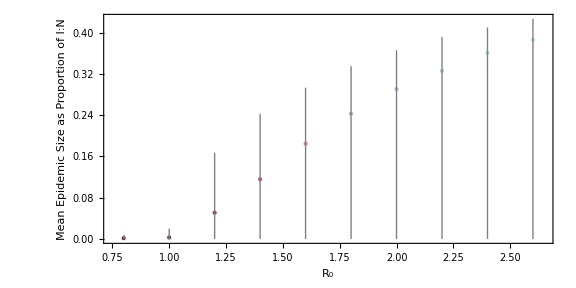

```mathematica
(* Helper for confidence intervals *)
CI95[data_] := Quantile[data, {0.025, 0.975}];

(* Epidemic size stats with 95% CI *)
MaxProportionInfectedStatsAssoc = Table[
  Module[{vals = simulationResults[r]["MaxProportionInfected"], ci},
    ci = CI95[vals];
    <|
      "R0" -> r,
      "MeanSize" -> N[Mean[vals]],
      "CI_Lower" -> N[ci[[1]]],
      "CI_Upper" -> N[ci[[2]]]
    |>
  ],
  {r, r0Values}
];
(* Colour palette *)
colorFunc = ColorData["CandyColors"];
meanSizes = MaxProportionInfectedStatsAssoc[[All, "MeanSize"]];
minSize = Min[meanSizes];
maxSize = Max[meanSizes];
normalizeSize[val_] := (val - minSize)/(maxSize - minSize);

(* Generate graphics elements *)
coloredSizePoints = Table[
  {
    colorFunc[normalizeSize[stat["MeanSize"]]],
    PointSize[Medium],
    Point[{stat["R0"], stat["MeanSize"]}],
    (* vertical error bar *)
    Gray,
    Line[{
      {stat["R0"], stat["CI_Lower"]},
      {stat["R0"], stat["CI_Upper"]}
    }]
  },
  {stat, MaxProportionInfectedStatsAssoc}
]
Graphics[
  coloredSizePoints /. PointSize[_] :> PointSize[Large],
  Frame -> True,
  FrameLabel -> {
    Style["R₀", 14],
    Style["Mean Epidemic Size as Proportion of I:N", 14]
  },
  PlotRange -> {{0.75, 2.65}, Automatic},
  AspectRatio -> 0.5,
  ImageSize -> Large,
  FrameTicks -> Automatic,
  GridLines -> None
]
```

#### What do the distributions of the values actually look like?

{1000,1000,2,1000,1000,1000,3,1000,2,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,4,1000,3,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,7,1000,1000,1000,1000,1000,1000,1000,1000,7,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,3,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,2,1000,1000,1000,3,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,5,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,3,1000,1000,1000,2,1000,1000,1000,1000,1000,4,1000,1000,1000,1000,3,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,2,1000,2,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,4,1000,1000,1000,7,1000,1000,1000,1000,1000,3,1000,7,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,6,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,3,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,1000,1000,1000,1000,1000,1000,5,1000,1000,1000,1000,1000,3,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,4,1000,1000,1000,1000,1000,1000,4,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,4,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,4,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,2,1000,1000,3,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,4,2,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,2,2,1000,3,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,2,3,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,7,2,1000,1000,2,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,3,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,2,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000}

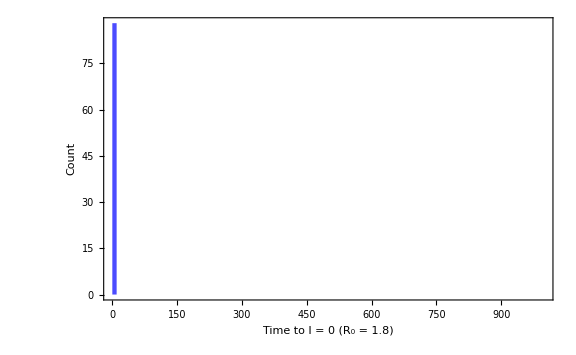

```mathematica
r = 1.8;
vals = simulationResults[r]["ExtinctionTimes"];
vals = Select[vals, # > 1 &]
Histogram[
  vals,
  {0, 1000, 10},  (* adjust bin size if needed *)
  "Count",
  Frame -> True,
  FrameLabel -> {
    "Time to I = 0 (R₀ = " <> ToString[r] <> ")",
    "Count"
  },
  ChartStyle -> Directive[Opacity[0.7], Blue],
  ImageSize -> Large
]
```

# This section is code I don’t really want for now

I want to see how changing our different components of our expression would change the expected R0

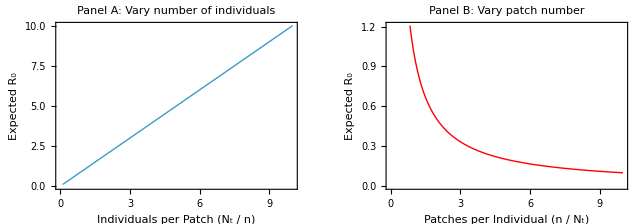
```mathematica
(* RESET AND DEFINE *)
ClearAll[initialInfected, ntRange, nRange, r0Formula, r0DensityData1, r0DensityData2]
initialInfected = 1;

(* Define fixed quantities *)
fixedN = 1000;
fixedNt = 1000;

(* FULL EXPRESSION *)
r0Formula[nt_, n_] := n * (1/n)^2 * (nt - initialInfected)  (* Equivalent to (nt - 1)/n *)

(* PANEL A: Vary Nt, fix n — plot vs. individuals per patch *)
ntRange = Range[100, 10000, 50];
r0DensityData1 = Table[
  {nt/fixedN, r0Formula[nt, fixedN]},   (* x = density *)
  {nt, ntRange}
];

(* PANEL B: Vary n, fix Nt — plot vs. patches per individual *)
nRange = Range[100, 10000, 50];
r0DensityData2 = Table[
  {n/fixedNt, r0Formula[fixedNt, n]},   (* x = inverse density *)
  {n, nRange}
];

(* PANEL A PLOT *)
panelA = ListLinePlot[
  r0DensityData1,
  Frame -> True,
  FrameLabel -> {
    Style["Individuals per Patch (Nₜ / n)", 14],
    Style["Expected R₀", 14]
  },
  PlotLabel -> 
    Style["Panel A: Vary number of individuals", 14, Bold],
  PlotStyle -> Thick,
  ImageSize -> 400
];

(* PANEL B PLOT *)
panelB = ListLinePlot[
  r0DensityData2,
  Frame -> True,
  FrameLabel -> {
    Style["Patches per Individual (n / Nₜ)", 14],
    Style["Expected R₀", 14]
  },
  PlotLabel -> 
    Style["Panel B: Vary patch number", 14, Bold],
  PlotStyle -> {Thick, Red},
  ImageSize -> 400
];

(* COMBINE PLOTS *)
GraphicsRow[{panelA, panelB}, Spacings -> 20]



-Graphics-
```